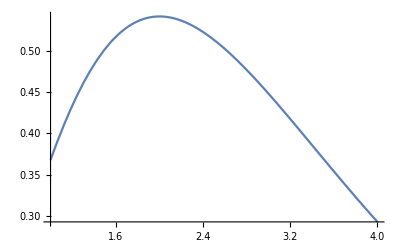

```mathematica
Plot[x^2*Exp[-x],{x,1,4}]
```

```mathematica
Integrate[x^2*Exp[-x],{x,1,4}]
N[%,10]
```

(-26+5 ⅇ^3)/ⅇ^4

1.363190595

```mathematica
Integrate[x^2*Exp[-x],{x,1,x}]
D[%,x]
%//Simplify
```

5/ⅇ-ⅇ^-x (2+x (2+x))

-ⅇ^-x (2+2 x)+ⅇ^-x (2+x (2+x))

ⅇ^-x x^2

```mathematica
g=x^2*Exp[-x];
a = 1;
b=4;
A=Integrate[g,{x,a,b}]
Plot[g,{x,a,b}]
k=1/A
f=k g
Integrate[f,{x,a,3}]
N[%,10]
Integrate[f,{x,a,b}]
EV=Integrate[x f,{x,a,b}]
EV//N
Var=Integrate[x^2 f,{x,a,b}]
Var//N
F=Integrate[f,{x,a,x}]
D[F,x]
D[F,x]//Simplify
f-D[F,x]//Simplify
```

(-26+5 ⅇ^3)/ⅇ^4

-Graphics-

ⅇ^4/(-26+5 ⅇ^3)

(ⅇ^(4-x) x^2)/(-26+5 ⅇ^3)

(ⅇ (-17+5 ⅇ^2))/(-26+5 ⅇ^3)

0.7284506271

1

(2 (-71+8 ⅇ^3))/(-26+5 ⅇ^3)

2.40997

13+486/(26-5 ⅇ^3)

6.47017

(5 ⅇ^3-ⅇ^(4-x) (2+x (2+x)))/(-26+5 ⅇ^3)

(-ⅇ^(4-x) (2+2 x)+ⅇ^(4-x) (2+x (2+x)))/(-26+5 ⅇ^3)

(ⅇ^(4-x) x^2)/(-26+5 ⅇ^3)

0

√(25-x^2)

(25 π)/4

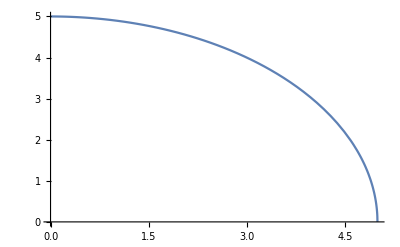

4/(25 π)

(4 √(25-x^2))/(25 π)

(24+50 ArcSin[3/5])/(25 π)

0.7152430201

1

20/(3 π)

2.12207

25/4

6.25

ConditionalExpression[(2 (x √(25-x^2)+25 ArcSin[x/5]))/(25 π),-5<Re[x]≤5||x∉ℝ]

ConditionalExpression[(2 (-x^2/(√(25-x^2))+√(25-x^2)+5/(√(1-x^2/25))))/(25 π),-5<Re[x]≤5||x∉ℝ]

ConditionalExpression[(4 √(25-x^2))/(25 π),-5<Re[x]≤5||x∉ℝ]

ConditionalExpression[0,-5<Re[x]≤5||x∉ℝ]

```mathematica
g=Sqrt[25-x^2]
a = 0;
b=5;
A=Integrate[g,{x,a,b}]
Plot[g,{x,a,b}]
k=1/A
f=k g
Integrate[f,{x,a,3}]
N[%,10]
Integrate[f,{x,a,b}]
EV=Integrate[x f,{x,a,b}]
EV//N
Var=Integrate[x^2 f,{x,a,b}]
Var//N
F=Integrate[f,{x,a,x}]
D[F,x]
D[F,x]//Simplify
f-D[F,x]//Simplify
```

Log[4]+Log[5]-(6 Log[6])/5

0.845621

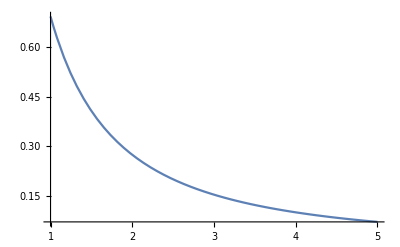

1/(Log[4]+Log[5]-(6 Log[6])/5)

Log[1+x]/(x^2 (Log[4]+Log[5]-(6 Log[6])/5))

(5 Log[27/4])/(3 Log[50000/729])

0.7527181038

1

-(5 (π^2+12 PolyLog[2,-5]))/(12 Log[50000/729])

2.27858

(5 (-4+Log[11664]))/Log[50000/729]

6.34358

ConditionalExpression[(5 (Log[4]+Log[x]-((1+x) Log[1+x])/x))/Log[50000/729],Re[x]>0||x∉ℝ]

ConditionalExpression[(5 (-Log[1+x]/x+((1+x) Log[1+x])/x^2))/Log[50000/729],Re[x]>0||x∉ℝ]

ConditionalExpression[(5 Log[1+x])/(x^2 Log[50000/729]),Re[x]>0||x∉ℝ]

ConditionalExpression[0,Re[x]>0||x∉ℝ]

```mathematica
g=Log[x+1]/x^2;
a = 1;
b=5;
A=Integrate[g,{x,a,b}]
%//N
Plot[g,{x,a,b}]
k=1/A
f=k g
Integrate[f,{x,a,3}]
N[%,10]
Integrate[f,{x,a,b}]
EV=Integrate[x f,{x,a,b}]
EV//N
Var=Integrate[x^2 f,{x,a,b}]
Var//N
F=Integrate[f,{x,a,x}]
D[F,x]
D[F,x]//Simplify
f-D[F,x]//Simplify
```